IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

230

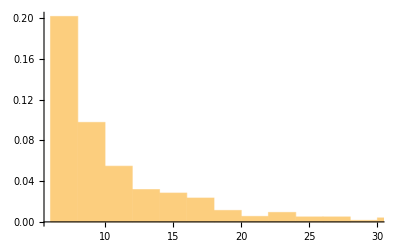

```mathematica
(* routine to *)
<<IGraphM`
Nn=(32)^2;(*number of spins*)mcs=40;(*Monte Carlo steps*)J=1;(*interaction strength*)
kT=Range[3.6,1,-0.2];(*range of temperatures*)NkT=Length[kT];
b=0;
this = 1;
While[(Mod[this,2]==1),
	γ = 2.9;
nodes = Nn;
k0 = 6;
kmax = Min[nodes-1,k0*nodes^(1/(γ-1))]; (* natural cut off *)
data=RandomVariate[TruncatedDistribution[{k0,kmax},ParetoDistribution[k0,γ-1]],nodes];
mythis = Total[yy];
yy = Floor[data];
this = Total[yy];]
Round[kmax]
Show[Histogram[yy,nodes,"PDF"],Plot[f[x],{x,k0,kmax}]];
graph=IGRealizeDegreeSequence[yy];
myA =AdjacencyMatrix[graph];
Histogram[VertexDegree[graph],100,"PDF"]
```

```mathematica
rewires = 1000000;
reGraph = IGRewire[graph,rewires];
myA =AdjacencyMatrix[reGraph];
graph = AdjacencyGraph[myA];
```

```mathematica
myRewire[flagIn_,nRew_,inputA2_,speedUpIn_]:=Module[{flag=flagIn,myRew=nRew,myA=inputA2,speedUp=speedUpIn},
(* if assortative*)
totalRew=0; nodeA = -1;nodeB = -1;nodeC = -1; nodeD = -1;
myArewAss = myA;
graphDegrees = VertexDegree@graph ;(*gives node to degree *)   kMax = Max[graphDegrees]; (* per normalizzare la p rewire*)
tries = myRew^2*10;curT=0;
poll = Table[i,{i,1,Nn}];
If[(speedUp==1),
Print["preferential pick enabled"];
prefPick = Sort[graphDegrees]; prefLowerPoll = Table[prefPick[[j]],{j,Nn -Ceiling[Nn-Sqrt[Nn]],Nn}];
poll = Table[0,{i,1,Length[prefLowerPoll]}];
For[k=1,k≤Length[prefLowerPoll],k++,
iterPoll = 1; 
While[prefLowerPoll[[k]]==graphDegrees[[iterPoll]],iterPoll++;];
poll[[k]] = iterPoll;]];
While[(totalRew< myRew && curT<tries),curT++;
nodeA = RandomChoice[poll]; nodeC = RandomInteger[{1,Nn}]; (*nodi rewire*)
nodeB = RandomInteger[{1,Nn}]; nodeD = RandomInteger[{1,Nn}];(*per velocizzare potrei selezionare in base al grado..*)
While[(Not[((nodeA≠ nodeB) && (nodeA ≠ nodeC) &&(nodeA≠ nodeD)&& (nodeB ≠ nodeC)&&(nodeB≠nodeD) &&(nodeC≠ nodeD))] ),
 nodeC = RandomInteger[{1,Nn}]; nodeB = RandomInteger[{1,Nn}];nodeD = RandomInteger[{1,Nn}];]; 
sorted=ReverseSort[{{graphDegrees[[nodeA]],nodeA},{graphDegrees[[nodeB]],nodeB},{graphDegrees[[nodeC]],nodeC},{graphDegrees[[nodeD]],nodeD}}];
If[(flag ==1),
nodeA     = sorted[[1]][[2]]; nodeC    =sorted[[2]][[2]]; nodeB     =sorted[[3]][[2]]; nodeD     =sorted[[4]][[2]],
nodeA     = sorted[[1]][[2]]; nodeB    =sorted[[2]][[2]]; nodeD     =sorted[[3]][[2]]; nodeC     =sorted[[4]][[2]]];
If[(myArewAss[[nodeB]][[nodeD]]==0) &&(myArewAss[[nodeA]][[nodeC]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeC]]=1; myArewAss[[nodeC]][[nodeA]]=1; myArewAss[[nodeB]][[nodeD]] = 1; myArewAss[[nodeD]][[nodeB]] = 1; 
totalRew++;
If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew]];];
If[Mod[curT,Ceiling[tries/10]]==0,Print["Current try: ", curT]; Print["Current Pearson: ", N@GraphAssortativity[ AdjacencyGraph[myArewAss]]]];];
Print["Total rewires: ", totalRew];]
```

```mathematica
myRewireEdge[flagIn_,nRew_,inputA2_]:=Module[{flag=flagIn,myRew=nRew,myA=inputA2},
(* if assortative*)
totalRew=0; nodeA = -1;nodeB = -1;nodeC = -1; nodeD = -1; edgeList = IGIndexEdgeList[graph];totalEdges = Length[edgeList];
edgeAlfa=-1;edgeBeta = -1;
myArewAss = myA;
graphDegrees = VertexDegree@graph ;(*gives node to degree *)   kMax = Max[graphDegrees]; (* per normalizzare la p rewire*)
tries = myRew^2*10;curT=0;
poll = Table[i,{i,1,Nn}];
Print["Flag is: ", flag];
Print["rewiring matrix with ass: ",N@GraphAssortativity[AdjacencyGraph[myArewAss]]];
While[(totalRew< myRew && curT<tries),curT++;
While[(edgeAlfa==edgeBeta ||nodeA==nodeB|| nodeA==nodeC || nodeA ==nodeD || nodeB==nodeC || nodeB==nodeD),
edgeAlfa = RandomInteger[{1,totalEdges}]; edgeBeta = RandomInteger[{1,totalEdges}];
(*controllo che siano diversi*)
nodeA = edgeList[[edgeAlfa]][[1]]; nodeB = edgeList[[edgeAlfa]][[2]]; (*nodi rewire*)
nodeC = edgeList[[edgeBeta]][[1]]; nodeD = edgeList[[edgeBeta]][[2]];];
(*per velocizzare potrei selezionare in base al grado..*)
sorted=ReverseSort[{{graphDegrees[[nodeA]],nodeA},{graphDegrees[[nodeB]],nodeB},{graphDegrees[[nodeC]],nodeC},{graphDegrees[[nodeD]],nodeD}}];
If[(flag ==1),
nodeA     = sorted[[1]][[2]]; nodeC    =sorted[[2]][[2]]; nodeB     =sorted[[3]][[2]]; nodeD     =sorted[[4]][[2]],
nodeA     = sorted[[1]][[2]]; nodeB    =sorted[[2]][[2]]; nodeD     =sorted[[3]][[2]]; nodeC     =sorted[[4]][[2]]];
If[(myArewAss[[nodeB]][[nodeD]]==0) &&(myArewAss[[nodeA]][[nodeC]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeC]]=1; myArewAss[[nodeC]][[nodeA]]=1; myArewAss[[nodeB]][[nodeD]] = 1; myArewAss[[nodeD]][[nodeB]] = 1; 
totalRew++;If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew];],
If[graphDegrees[[nodeC]]==graphDegrees[[nodeD]],tmp = nodeC;nodeC=nodeD;nodeD=tmp;
If[(myArewAss[[nodeB]][[nodeD]]==0) &&(myArewAss[[nodeA]][[nodeC]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeC]]=1; myArewAss[[nodeC]][[nodeA]]=1; myArewAss[[nodeB]][[nodeD]] = 1; myArewAss[[nodeD]][[nodeB]] = 1; 
totalRew++;If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew];];];];];
If[Mod[curT,Ceiling[tries/10]]==0,Print["Current try: ", curT]; Print["Current Pearson: ", N@GraphAssortativity[AdjacencyGraph[myArewAss]]]];
nodeA=-1;nodeB=-1;];
Print["Total rewires: ", totalRew];]
```

```mathematica
plotAdjMatrix[myAStar_]:=Module[{myA=myAStar},
graph = AdjacencyGraph[myArewAss];
graphDegrees = VertexDegree@graph;
mapDegreeNode = Table[{graphDegrees[[i]],i},{i,1,Nn}];
mapDegreeNode = Sort[mapDegreeNode];
adjancySorted = Table[Table[0,{jjj,1,Nn}],{kkk,1,Nn}];
For[k=1,k<=Nn,k++,
For[l=1,l<k,l++,
If[myA[[ mapDegreeNode[[k]][[2]] ]][[mapDegreeNode[[l]][[2]]]] ==1,
adjancySorted[[k]][[l]] = 1;
adjancySorted[[l]][[k]] = 1;
];]];
For[k=1,k<=Nn,k++,
For[l=1,l<k,l++,
If[myA[[ mapDegreeNode[[k]][[2]] ]][[mapDegreeNode[[l]][[2]]]] ==-1,
adjancySorted[[k]][[l]] = -1;
adjancySorted[[l]][[k]] = -1;
];]];
MatrixPlot[adjancySorted,ColorRules->{1->Red,-1->Blue}]
]
```

```mathematica
myLines[myAinput_,maxLinesInput_]:=Module[{myA=myAinput,maxLines=maxLinesInput},
graph = AdjacencyGraph[myA];
graphDegrees = VertexDegree@graph;
levels = BinCounts[Sort[graphDegrees]];
length = Length[levels];
count = 0;
iter = 1;
lines = Table[0,{i,1,maxLinesInput}];
For[k=1,k<=length,k++,
If[levels[[k]]≠0 && iter <= maxLines,lines[[iter]]=levels[[k]]+count; iter++; count = levels[[k]]+count;]
]]
```

```mathematica
(*Export["/home/albertoartoni/Desktop/Discussione/Immagini/Esempio4/reteLast.dat",myArewAss];*)

myArewAss =Import["/home/albertoartoni/Desktop/Discussione/Immagini/Esempio4/reteLastGiovedi.dat"];
myAinit = myArewAss;
```

```mathematica
For[kk=1, kk≤Nn,kk++,
If[myArewAss[[kk,kk]]==1, Print["loop"];];]
```

```mathematica
myAtemp = myArewAss;
N@GraphAssortativity[AdjacencyGraph[myArewAss]]
Timing[myRewireGreedyAssk0[1,2000,myArewAss,0]]
Timing[myRewireGreedyAssk1[1,2000,myArewAss,0]]
Timing[myRewireGreedyAssk2[1,2000,myArewAss,0]]
Timing[myRewireEdge[1,5000,myArewAss]]
For[kk=1, kk≤Nn,kk++,
If[myArewAss[[kk,kk]]==1, Print["loop"];];]
```

```mathematica
myLines[myArewAss,4];
lines
plotAdjMatrix[myArewAss]
MatrixPlot[adjancySorted,Mesh->{lines,lines},MaxPlotPoints->Infinity]
```

```mathematica
AdjacencyGraph[myArewAss]
myLines[myArewAss,5]
lines
```

{200,327,435,516,578}

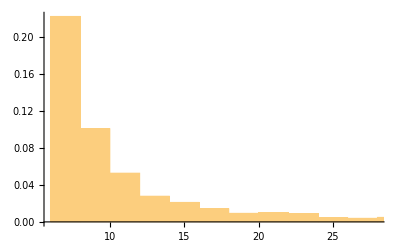

```mathematica
Histogram[VertexDegree[graph],100,"PDF"]
```

```mathematica
myRewireGreedyAssk0[flagIn_,nRew_,inputA2_,speedUpIn_]:=Module[{flag=flagIn,myRew=nRew,myA=inputA2,speedUp=speedUpIn},
(* if assortative*)
totalRew=0; nodeA = -1;nodeB = -1;nodeC = -1; nodeD = -1;
myArewAss = myA;
graphDegrees = VertexDegree@graph ;(*gives node to degree *)   kMax = Max[graphDegrees]; (* per normalizzare la p rewire*)
mapDegreeNodeRev = ReverseSort[Table[{graphDegrees[[i]],i},{i,1,Nn}]];
tries = myRew^2*10;curT=0;
While[(totalRew< myRew && curT<tries),curT++;
nodeAidx = RandomInteger[{1,Nn-3}];nodeBidx = RandomInteger[{nodeAidx+1,Nn-2}]; nodeCidx = RandomInteger[{nodeBidx+1,Nn-1}]; (*nodi rewire*)
 nodeDidx = RandomInteger[{nodeCidx+1,Nn}];(*per velocizzare potrei selezionare in base al grado..*) 
nodeA = mapDegreeNodeRev[[nodeAidx]][[2]];nodeD = mapDegreeNodeRev[[nodeBidx]][[2]];nodeC = mapDegreeNodeRev[[nodeCidx]][[2]];
nodeB = mapDegreeNodeRev[[nodeDidx]][[2]];
If[(myArewAss[[nodeB]][[nodeC]]==0) &&(myArewAss[[nodeA]][[nodeD]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeD]]=1; myArewAss[[nodeD]][[nodeA]]=1; myArewAss[[nodeB]][[nodeC]] = 1; myArewAss[[nodeC]][[nodeB]] = 1; 
totalRew++;
If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew]]
];
If[Mod[curT,Ceiling[tries/10]]==0,Print["Current try: ", curT]; Print["Current Pearson: ", N@GraphAssortativity[ AdjacencyGraph[myArewAss]]]];];
Print["Total rewires: ", totalRew];]
myRewireGreedyAssk1[flagIn_,nRew_,inputA2_,speedUpIn_]:=Module[{flag=flagIn,myRew=nRew,myA=inputA2,speedUp=speedUpIn},
(* if assortative*)
totalRew=0; nodeA = -1;nodeB = -1;nodeC = -1; nodeD = -1;
myArewAss = myA;
graphDegrees = VertexDegree@graph ;(*gives node to degree *)   kMax = Max[graphDegrees]; (* per normalizzare la p rewire*)
mapDegreeNodeRev = ReverseSort[Table[{graphDegrees[[i]],i},{i,1,Nn}]];
tries = myRew^2*10;curT=0;
While[(totalRew< myRew && curT<tries),curT++;
nodeAidx = RandomInteger[{1,Nn-3}];nodeBidx = RandomInteger[{nodeAidx+1,Nn-2}]; nodeCidx = RandomInteger[{nodeBidx+1,Nn-1}]; (*nodi rewire*)
 nodeDidx = RandomInteger[{nodeCidx+1,Nn}];(*per velocizzare potrei selezionare in base al grado..*) 
nodeA = mapDegreeNodeRev[[nodeAidx]][[2]];nodeD = mapDegreeNodeRev[[nodeBidx]][[2]];nodeC = mapDegreeNodeRev[[nodeCidx]][[2]];
nodeB = mapDegreeNodeRev[[nodeDidx]][[2]];
If[(myArewAss[[nodeB]][[nodeC]]==0) &&(myArewAss[[nodeA]][[nodeD]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeD]]=1; myArewAss[[nodeD]][[nodeA]]=1; myArewAss[[nodeB]][[nodeC]] = 1; myArewAss[[nodeC]][[nodeB]] = 1; 
totalRew++;
If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew]]
];
If[Mod[curT,Ceiling[tries/10]]==0,Print["Current try: ", curT]; Print["Current Pearson: ", N@GraphAssortativity[ AdjacencyGraph[myArewAss]]]];];
Print["Total rewires: ", totalRew];]
(* attento*)
myRewireGreedyAssk2[flagIn_,nRew_,inputA2_,speedUpIn_]:=Module[{flag=flagIn,myRew=nRew,myA=inputA2,speedUp=speedUpIn},
(* if assortative*)
set = 200+127+108+81+62+52+50;kCur = 50;offSet = 50;
totalRew=0; nodeA = -1;nodeB = -1;nodeC = -1; nodeD = -1;
myArewAss = myA;
graphDegrees = VertexDegree@graph ;(*gives node to degree *)   kMax = Max[graphDegrees]; (* per normalizzare la p rewire*)
mapDegreeNodeRev = ReverseSort[Table[{graphDegrees[[i]],i},{i,1,Nn}]];
tries = myRew^2*10;curT=0;
While[(totalRew< myRew && curT<tries),curT++;
nodeAidx = RandomInteger[{1,53-3}]; nodeBidx = RandomInteger[{Nn-set-kCur,Nn-set-2+offSet}]; nodeCidx = RandomInteger[{nodeBidx+1,Nn-set-1+offSet}]; (*nodi rewire*)
 nodeDidx = RandomInteger[{nodeCidx+1,Nn-set+offSet}];(*per velocizzare potrei selezionare in base al grado..*) 
nodeA = mapDegreeNodeRev[[nodeAidx]][[2]];nodeD = mapDegreeNodeRev[[nodeBidx]][[2]];nodeC = mapDegreeNodeRev[[nodeCidx]][[2]];
nodeB = mapDegreeNodeRev[[nodeDidx]][[2]];
If[(myArewAss[[nodeB]][[nodeC]]==0) &&(myArewAss[[nodeA]][[nodeD]] == 0)&&(myArewAss[[nodeC]][[nodeD]] == 1)&&(myArewAss[[nodeA]][[nodeB]] == 1),
myArewAss[[nodeA]][[nodeB]]=0; myArewAss[[nodeB]][[nodeA]]=0; myArewAss[[nodeC]][[nodeD]] = 0; myArewAss[[nodeD]][[nodeC]] = 0;
myArewAss[[nodeA]][[nodeD]]=1; myArewAss[[nodeD]][[nodeA]]=1; myArewAss[[nodeB]][[nodeC]] = 1; myArewAss[[nodeC]][[nodeB]] = 1; 
totalRew++;
If[Mod[totalRew,Ceiling[myRew/10]]==0,Print["Current rewire: ", totalRew]]
];
If[Mod[curT,Ceiling[tries/10]]==0,Print["Current try: ", curT]; Print["Current Pearson: ", N@GraphAssortativity[ AdjacencyGraph[myArewAss]]]];];
Print["Total rewires: ", totalRew];]
```

```mathematica
BinCounts[graphDegrees]
```

```mathematica
myAtemp = myArewAss;
Timing[myRewireGreedyAssk1[0,1000,myArewAss,0]]
```

```mathematica
Nn = 1024;
plotAdjMatrix[myAtemp]
plotAdjMatrix[myArewAss];
MatrixPlot[adjancySorted,Mesh->{{set-offSet,set+kCur},{set-offSet,set+kCur}}]
```

```mathematica
myArewAss = myAinit ;
```

```mathematica
myAtemp = myArewAss;
vett = {400,600,800,1024};
For[k=1,k≤Length[vett],k++,
Nn = vett[[k]];
Timing[myRewireGreedyAssk1[0,2*Nn,myArewAss,0]]]
```

$Aborted

```mathematica
Export["/home/albertoartoni/Desktop/Discussione/Immagini/Esempio4/reteLastGiovedi.dat",myArewAss];
```